```mathematica
f=y^2 Log[x y]^3+ 4 π y Log[x y]^2+ (4 π)^2
f0=y Log[x y]+ 4 π 
fadv=If[x y>0.1,y^2 Log[x y]^3+ 4 π y Log[x y]^2+ (4 π)^2-func[x y] y  Log[ x y]^3,y^2 Log[x y]^3+ 4 π y Log[x y]^2+ (4 π)^2]
```

16 π^2+4 π y Log[x y]^2+y^2 Log[x y]^3

4 π+y Log[x y]

If[x y>0.1,y^2 Log[x y]^3+4 π y Log[x y]^2+(4 π)^2-func[x y] y Log[x y]^3,y^2 Log[x y]^3+4 π y Log[x y]^2+(4 π)^2]

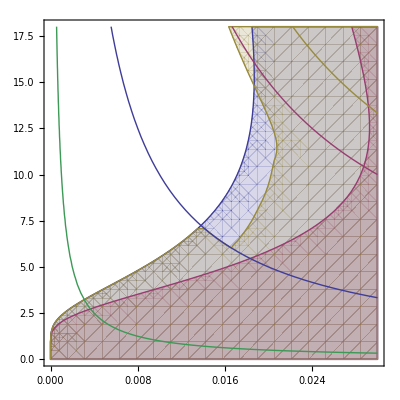

```mathematica
Show[RegionPlot[{f>0, f0>0, fadv>0}, {x,0.0,0.03},{y, 0.0, 18}],ContourPlot[{x y==0.1,x y==0.3 ,x y==0.4,x y==0.0  },{x,0.0,0.03},{y, 0.0, 18}]]
```

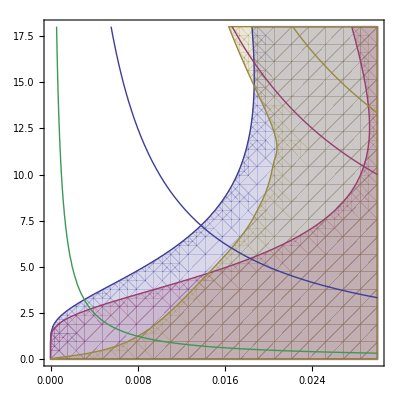

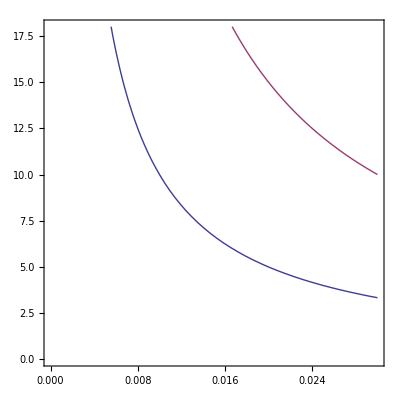

```mathematica
upp
```

{x y==0.025,x y==0.05,x y==0.075,x y==0.1}

```mathematica
dotes={{0.01,-9.05909557851},{0.01259,-7.72770556439},{0.01585,-6.64668606378},{0.01995,-5.76698696404},{0.02512,-5.04886159165},{0.03162,-4.46227684234},{0.03981,-3.98606905757},{0.05012,-3.60704478888},{0.0631,-3.31993349456},{0.07943,-3.12612032754},{0.1,-1.58554703651},{0.11,-1.57521412942},{0.12,-1.57400413575},{0.14,-1.58229589095},{0.16,-1.60299899854},{0.17,-1.64108244368},{0.19,-1.7048831702},{0.22,-1.80861715364},{0.24,-1.95203594638},{0.27,-0.687068233085}}
```

{{0.01,-9.0591},{0.01259,-7.72771},{0.01585,-6.64669},{0.01995,-5.76699},{0.02512,-5.04886},{0.03162,-4.46228},{0.03981,-3.98607},{0.05012,-3.60704},{0.0631,-3.31993},{0.07943,-3.12612},{0.1,-1.58555},{0.11,-1.57521},{0.12,-1.574},{0.14,-1.5823},{0.16,-1.603},{0.17,-1.64108},{0.19,-1.70488},{0.22,-1.80862},{0.24,-1.95204},{0.27,-0.687068}}

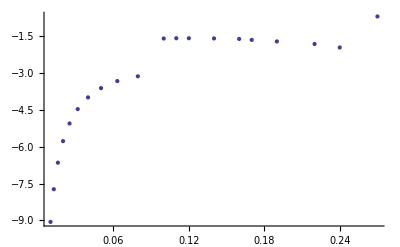

```mathematica
ListPlot[dotes]
```

```mathematica
func=Interpolation[dotes]
```

InterpolatingFunction[{{0.01,0.27}},<>]

InterpolatingFunction::dmval: Input value {1.498838060941828`*^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

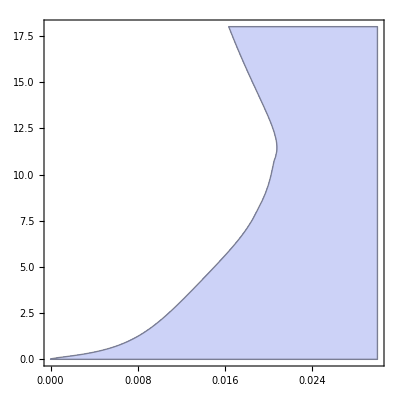

```mathematica
RegionPlot[fadv>0, {x,0.0,0.03},{y, 0.0, 18}]
```